```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/data_v2/low_mub

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,0,800,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,0,800,10}];
r422=chi4/chi2;
r422[[3]]=r422[[4]];
r422[[1;;35]][[1;;60]]=1;
r422[[36;;55]][[1;;40]]=1;
r422[[56;;65]][[1;;30]]=1;
r422[[66;;72]][[1;;25]]=1;
r422[[73;;78]][[1;;15]]=1;
r422[[79;;81]][[1;;13]]=1;
```

```mathematica
mub=Table[i,{i,0,800,10}];
T=Table[i,{i,1,120,1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r422[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
(*Export["r42high.dat",R42all]*)
```

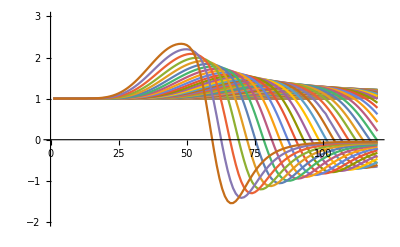

```mathematica
ListLinePlot[r422,PlotRange->{{0,120},{-2,3}}]
```

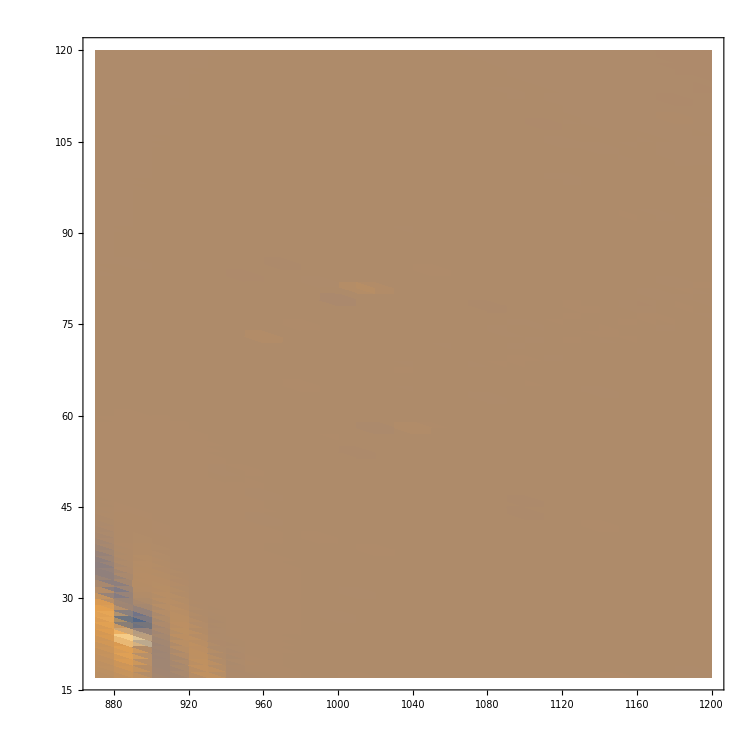

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-25,40}}]
```